```mathematica
g=9.8; (*grav. constant*)

v =30 
th = 50 * pi /180
x[0]=0
y[0] = 2
x'[0] =V Cos[th]
y'[0] = V Sin[th]
odelx={x''[t] == (-g x'[t]/v t^2) Sqrt[x'[t]^2 y'[t]^2]};
odely={y''[t] == -g (1 + ( y'[t]/v t^2)) Sqrt[x'[t]^2 y'[t]^2]};
solx=NDSolve[ode1x,x,x',{t,0,200}];
soly=NDSolve[odely,y,y',{t,0,200}];
```

30

(5 pi)/18

0

2

V Cos[(5 pi)/18]

V Sin[(5 pi)/18]

NDSolve::deqn: Equation or list of equations expected instead of ode1x in the first argument ode1x.

NDSolve::derlen: The length of the derivative operator Derivative[2] in SuperscriptBox[ is not the same as the number of arguments.

```mathematica
myplot1 = Plot[(180/Pi) θ[t]/.sol,{t,0,20},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
omega=√(g/l);
```

```mathematica
approx = (180/Pi) θ0 Cos[omega*t];
myplot2=Plot[approx,{t,0,200},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];
```

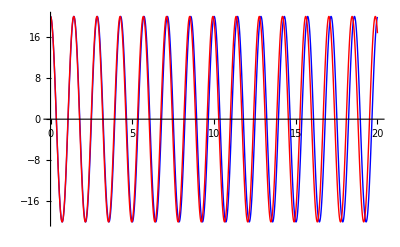

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```